```mathematica
Clear["Global`*"]
(*Defififinition of f=f(x,t)*)
f1[x_,y_,t_]= -x + Exp[t];
f2[x_,y_,t_]= t Exp[-t^2]-2t x;
(*Error message*)
approximate::nonnegativeint="'N' must be replaced by a non-negative integer.";

(*Construction of successively approximate sequences t:time;x0:initial value;N:number of iterations The initial time t0 is always 0*)

approximate[t_,x0_,y0_,N_]:=Module[{k=0}, If[Or[N<0,Not[IntegerQ[N]]],Message[approximate::nonnegativeint,N],
x[0,s_]:=x0;
y[0,s_]:= y0;
While[k<N,
x[k_,s_]:=(x[k,s]=x0+Integrate[f1[x[k−1,u],y[k-1,u],u],{u,0,s}]);
y[k_,s_]:=(y[k,s]=y0+Integrate[f2[x[k-1,u],y[k-1,u],u],{u,0,s}]) ;
k++];(*Instead of “While,” you can also use “For” and “Do”*)
y[N,t]
]
];
(*An example of “approximate”*)
approximate[1,1,1,3]
```

1-(2+3 ⅇ)/(4 ⅇ)

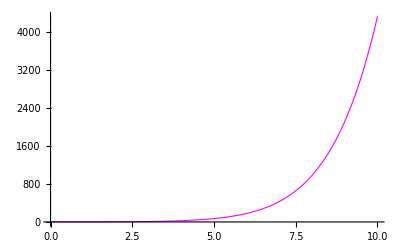

```mathematica
(*Numerical solution (data):k=number of iterations;d=[step size];tlast=[last time]*)nsol[k_,d_,x0_,tlast_]:=Table[{t,approximate[t,x0,k]},{t,0,tlast,d}];
ngraph[k_,d_,x0_,tlast_]:=ListLinePlot[nsol[k,d,x0,tlast],PlotStyle->{Thickness[0.002],RGBColor[1,0,1]},PlotRange->All];
(*Graph of the numerical solution:k=3;d=0:1;x0=1;tlast=10*)
ngraph[8,0.1,1,10]
```

```mathematica
(*Analytical solution:x0=1*)
asol[x0_,y0_]:=DSolve[{x '[t]==f1[x[t],y[t],t],y'[t]==f2[x[t],y[t],t],x[0]==x0,y[0]==y0},{x[t],y[t]},t];
asol[1,1]
```

{{x[t]→(2 √π Cos[2 √π t]+Sin[2 √π t])/(2 √π),y[t]→Cos[2 √π t]-2 √π Sin[2 √π t]}}

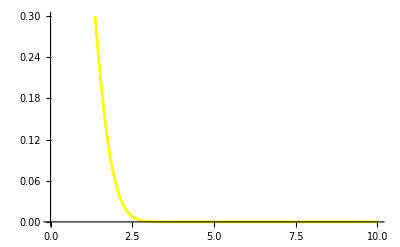

```mathematica
(*Graph of the analytical solution:x0=1;tlast=10*) agraph[x0_,tlast_]:=Plot[Evaluate[x[t]/.asol[x0]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,1,0]}]
agraph[1,10]
```

```mathematica
Show[agraph[1,10],ngraph[20,0.1,1,10]]
```

-Graphics-

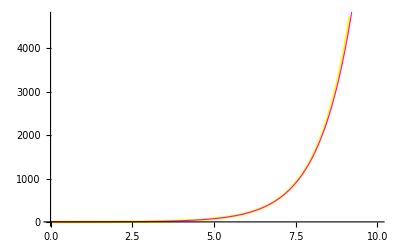

```mathematica
Show[agraph[1,10],ngraph[14,0.1,1,10]]
```

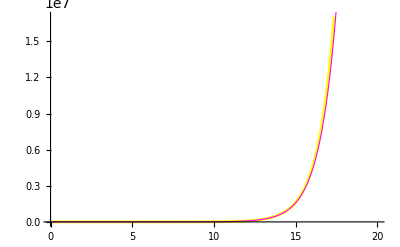

```mathematica
Show[agraph[1,20],ngraph[22,0.1,1,20]]
```

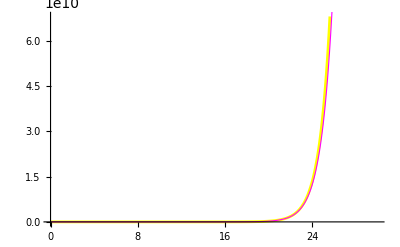

```mathematica
Show[agraph[1,30],ngraph[30,0.1,1,30]]
```